```mathematica
Subscript[p, k]=UnitStep[k-.5]*k^-τ E^(-k/ξ); Subscript[p, k] = Subscript[p, k]/Sum[Subscript[p, k],{k,0,∞}]
taus=Table[{τ->val},{val,1,5/2,1/2}]
ndists=Length[taus];
```

(ⅇ^(-k/ξ) k^-τ UnitStep[-0.5+k])/PolyLog[τ,ⅇ^(-1./ξ)]

{{τ→1},{τ→3/2},{τ→2},{τ→5/2}}

```mathematica
datapoints={Import["~/Codello/graphs/main/output/giant_tau=1.00_nodes=1000000",{}],
	Import["~/Codello/graphs/main/output/giant_tau=1.50_nodes=1000000"],
	Import["~/Codello/graphs/main/output/giant_tau=2.00_nodes=1000000"],
	Import["~/Codello/graphs/main/output/giant_tau=2.50_nodes=1000000"]};
pts=Length[datapoints[[1]]];
(* i -> index of file;
   j -> index of ξ;
   1,2 -> ξ, Subscript[P, ξ]. *)
datapoints=Table[{datapoints[[i]][[j]][[1]],datapoints[[i]][[j]][[2]]},{i,ndists},{j,pts}];
```

```mathematica
MatrixForm[datapoints]
```

((1.
0.000063) | (1.51991
0.041872) | (2.31013
0.299724) | (3.51119
0.463621) | (5.3367
0.570847) | (8.11131
0.643943) | (12.3285
0.695635) | (18.7382
0.733801) | (28.4804
0.762971) | (43.2876
0.785946) | (65.7933
0.8046) | (100.
0.819963)
(1.
0.000032) | (1.51991
0.000152) | (2.31013
0.092552) | (3.51119
0.279616) | (5.3367
0.404524) | (8.11131
0.489687) | (12.3285
0.548862) | (18.7382
0.591057) | (28.4804
0.621663) | (43.2876
0.644524) | (65.7933
0.661581) | (100.
0.674662)
(1.
0.00002) | (1.51991
0.000049) | (2.31013
0.000223) | (3.51119
0.066687) | (5.3367
0.201648) | (8.11131
0.296666) | (12.3285
0.364363) | (18.7382
0.41347) | (28.4804
0.449503) | (43.2876
0.476646) | (65.7933
0.49719) | (100.
0.513147)
(1.
0.000015) | (1.51991
0.000027) | (2.31013
0.00006) | (3.51119
0.000182) | (5.3367
0.00294) | (8.11131
0.08482) | (12.3285
0.150448) | (18.7382
0.198994) | (28.4804
0.23479) | (43.2876
0.261491) | (65.7933
0.281756) | (100.
0.297165))

```mathematica
gendeg=GeneratingFunction[Subscript[p, k],k,z]/.taus//FullSimplify
avg=D[gendeg,z]/.z->1
genexc=D[gendeg,z]/avg //FullSimplify
```

{(1. Log[1-ⅇ^(-1./ξ) z])/Log[1-ⅇ^(-1./ξ)],PolyLog[3/2,ⅇ^(-1./ξ) z]/PolyLog[3/2,ⅇ^(-1./ξ)],PolyLog[2,ⅇ^(-1./ξ) z]/PolyLog[2,ⅇ^(-1./ξ)],PolyLog[5/2,ⅇ^(-1./ξ) z]/PolyLog[5/2,ⅇ^(-1./ξ)]}

{-(1. ⅇ^(-1./ξ))/((1-ⅇ^(-1./ξ)) Log[1-ⅇ^(-1./ξ)]),(1. PolyLog[1/2,ⅇ^(-1./ξ)])/PolyLog[3/2,ⅇ^(-1./ξ)],-(1. Log[1-2.71828^(-1./ξ)])/PolyLog[2,ⅇ^(-1./ξ)],(1. PolyLog[3/2,ⅇ^(-1./ξ)])/PolyLog[5/2,ⅇ^(-1./ξ)]}

{1.+(-1.+1. z)/(1. ⅇ^(1./ξ)-1. z),(1. PolyLog[1/2,ⅇ^(-1./ξ) z])/(z PolyLog[1/2,ⅇ^(-1./ξ)]),(1. Log[1-ⅇ^(-1./ξ) z])/(z Log[1-ⅇ^(-1./ξ)]),(1. PolyLog[3/2,ⅇ^(-1./ξ) z])/(z PolyLog[3/2,ⅇ^(-1./ξ)])}

```mathematica
(*crit=Table[ξ/.NSolve[1==D[genexc[[i]],z]/.z->1,ξ,Reals]//First,{i,1,ndists}]*)
```

```mathematica
Clear[ξ]
gendeg[[1]]
genexc[[1]]
```

(1. Log[1-ⅇ^(-1./ξ) z])/Log[1-ⅇ^(-1./ξ)]

1.+(-1.+1. z)/(1. ⅇ^(1./ξ)-1. z)

```mathematica
Clear[P]
```

```mathematica
P[c_?NumericQ]:=(*Table[*)
1-gendeg[[1]]/.FindRoot[z==genexc[[1]],z,Reals(*,{z,0,0,1}*)(*,GenerateConditions->False*)]
(*,{i,1,ndists}]*)
```

```mathematica
P[1]
```

FindRoot::fdssnv: Search specification z without variables should be a list with 1 to 4 elements.

Join::heads: Heads List and FindRoot at positions 1 and 2 are expected to be the same.

ReplaceAll::reps: {Join[{ξ → 1}, FindRoot[z == genexc ⟦ 1 ⟧, z, Reals]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

1-(1. Log[1-ⅇ^(-1./ξ) z])/Log[1-ⅇ^(-1./ξ)]/.Join[{ξ→1},FindRoot[z==genexc⟦1⟧,z,Reals]]

```mathematica
ξ=1
```

1

```mathematica
FindRoot[z==genexc[[1]],{z,0,0,1}(*,GenerateConditions->False*)]
```

{z→1.}

```mathematica
analyticplot=LogLinearPlot[P[ξ],{ξ,1,100}]
```

-Graphics-

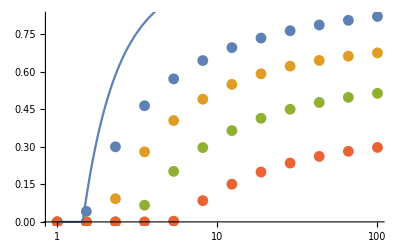

```mathematica
Show[{dataplot,analyticplot}]
```